```mathematica
Needs["GraphStore`"]
```

```mathematica
MSCStore = 
 CloudImport[
  "https://www.wolframcloud.com/env/0626c3e2-073a-4ec4-80f9-\
01e848d831aa", "WL"];
```

```mathematica
concepts = MSCStore // SPARQLQuery[
   SPARQLSelect[{ (* This first query finds subjects with codes *)
     RDFTriple[
      SPARQLVariable["concept"],
      URL["http://www.w3.org/2004/02/skos/core#notation"],
      SPARQLVariable["code"]
      ], (* The second query finds subjects with labels *)
     RDFTriple[
      SPARQLVariable["concept"],
      URL["http://www.w3.org/2004/02/skos/core#prefLabel"],
      SPARQLVariable["label"]
      ], (* 
     The third query finds subjects that are Concepts in the SKOS \
language *)
     RDFTriple[
      SPARQLVariable["concept"],
      URL["http://www.w3.org/1999/02/22-rdf-syntax-ns#type"],
      URL["http://www.w3.org/2004/02/skos/core#Concept"]
      ], (* So now we only have concepts with their code and label, 
     but we want only the English language labels *)
     SPARQLFilter[
      SPARQLEvaluation["langMatches"][
       SPARQLEvaluation["lang"][SPARQLVariable["label"]], "en"]]
     }
    ]];
```

```mathematica
classPairs = {("label" /. concepts // 
     Map[First]), ("code" /. concepts // Map[First] // 
     Map[Curry[StringTake][2]])} // Transpose;
```

```mathematica
exclude1 = 
  Select[classPairs, 
   StringMatchQ[#[[1]], ___ ~~ "Proceedings" ~~ ___] &];
exclude2 = 
  Select[classPairs, 
   StringMatchQ[#[[1]], ___ ~~ "Historical" ~~ ___] &];
exclude3 = 
  Select[classPairs, 
   StringMatchQ[#[[1]], ___ ~~ "General reference" ~~ ___] &];
exclude4 = 
  Select[classPairs, 
   StringMatchQ[#[[1]], ___ ~~ "Computational methods"] &];
exclude5 = 
  Select[classPairs, 
   StringMatchQ[#[[1]], ___ ~~ "Instructional" ~~ ___] &];
exclude6 = 
  Select[classPairs, StringMatchQ[#[[1]], ___ ~~ "Explicit" ~~ ___] &];
exclude7 = 
  Select[classPairs, 
   StringMatchQ[#[[1]], ___ ~~ "Experimental" ~~ ___] &];
exclude8 = 
  Select[classPairs, StringMatchQ[#[[1]], ___ ~~ "Research" ~~ ___] &];
exclude9 = 
  Select[classPairs, 
   StringMatchQ[#[[1]], ___ ~~ "None of the above" ~~ ___] &];
exclude = 
  Join[exclude1, exclude2, exclude3, exclude4, exclude5, exclude6, 
   exclude7, exclude8, exclude9];
trainingPairs = DeleteElements[classPairs, exclude];
```

```mathematica
trainingData = trainingPairs // MapApply[Rule];
```

```mathematica
classes = trainingData // Map[Last] // DeleteDuplicates
```

{00,01,03,05,06,08,11,12,13,14,15,16,17,18,19,20,22,26,28,30,31,32,33,34,35,37,39,40,41,42,43,44,45,46,47,49,51,52,53,54,55,57,58,60,62,65,68,70,74,76,78,80,81,82,83,85,86,90,91,92,93,94,97}

```mathematica
classifier = Classify[trainingData]
```

ClassifierFunction[…]

Starting our actual functions:

```mathematica
msc[code_] := "http://msc2010.org/resources/MSC/2010/" <> code <> "AXX";
```

And our actual stuff:

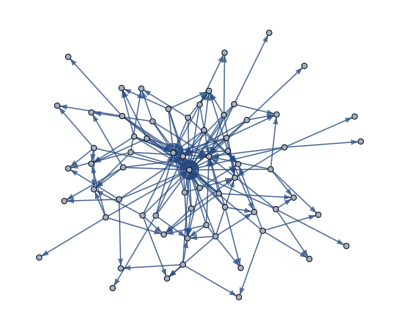

```mathematica
MTH = Import["to_import.m"];
categories = {#[[1]], #[[2]]//classifier}&/@MTH;
Function[code,RDFTriple[ex[#[[1]]],ex["uses"],msc[code]]]/@Commonest[#[[2]],5]&/@categories//Flatten//RDFStore//RDFGraph
```

```mathematica
filterOther[store_]:=store//SPARQLSelect[
     RDFTriple[SPARQLVariable["s"], SPARQLVariable["p"], 
      SPARQLVariable["o"]]
     ] // Map[Function[
{#s, #p,(Function[r,StringReplace[#o,r->"2010/"<>StringPart[r,{6,7}]<>"XXX"]]/@StringCases[#o, RegularExpression["2010/\d\d[A-Z]\d\d"]] // Append[#o])[[1]]}
     ]]//Select[#[[2]]==ex["uses"]&]//DeleteDuplicates;
```

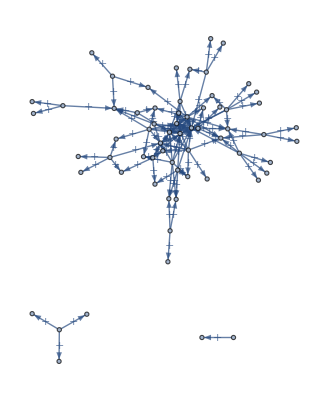

```mathematica
g1=filterOther[CloudImport["https://www.wolframcloud.com/env/e5c61039-81b9-49d6-8032-46e848745bd6", "WL"]];(*Ben White*)
g2=filterOther[CloudImport["https://www.wolframcloud.com/obj/6e83321c-6e9e-496b-aa5f-1f4a1a5995d4", "WL"]];(*Holly Barber*)
g3=filterOther[(CloudImport["https://www.wolframcloud.com/obj/d205a732-06d2-4499-8180-1aa79906a7ef", "Notebook"]//NotebookImport//ReleaseHold)[[1]]];(*Lucie Johnson*)
g4=filterOther[CloudImport["https://www.wolframcloud.com/env/1ff93e1f-5a29-4ba4-a087-0bc56d3f8134", "WL"]];(*Luke Garner*)
Flatten[Join[{g1,g2,g3,g4}],{1,2}]//RDFStore//RDFGraph//TooltipGraph
```